```mathematica
Needs["VariationalMethods`"]
Quit;
Clear;
```

```mathematica
Action=Sqrt[r[x]^2+2r'[x]v'[x]-(r[x]^2-m[v[x]])v'[x]^2]; (*Action functional (eqn4.5)*)
```

```mathematica
FullSimplify[EulerEquations[Action,v[x],x]] (*EL equation for v*)
```

(-4 r[x]^3 r'[x] v'[x] (-1+v'[x]^2)+2 r[x] r'[x] ((1+Tanh[3 v[x]]) v'[x] (1+v'[x]^2)+r'[x] (2+6 v'[x]^2))+4 r[x]^4 v''[x]-r[x]^2 (3 Sech[3 v[x]]^2 v'[x]^2+4 r''[x]+2 (1+Tanh[3 v[x]]) v''[x])+r'[x] (-3 Sech[3 v[x]]^2 v'[x]^3-4 v'[x] r''[x]+4 r'[x] v''[x]))/(√(2 r[x]^2+4 r'[x] v'[x]+(1-2 r[x]^2+Tanh[3 v[x]]) v'[x]^2))==0

```mathematica
FullSimplify[EulerEquations[Action,r[x],x]] (*EL equation for r*)
```

(-2 r[x] v'[x] (6 r'[x]+(1+Tanh[3 v[x]]) v'[x]) (-1+v'[x]^2)+4 r[x]^3 (-1+v'[x]^2)^2-4 r[x]^2 v''[x]+v'[x] (3 Sech[3 v[x]]^2 v'[x]^3+4 v'[x] r''[x]-4 r'[x] v''[x]))/(√(2 r[x]^2+4 r'[x] v'[x]+(1-2 r[x]^2+Tanh[3 v[x]]) v'[x]^2))==0

```mathematica
FullSimplify[Eliminate[{EulerEquations[Action,v[x],x],EulerEquations[Action,r[x],x],r[x]^4/Subscript[r, 0]^2==r[x]^2+2 r'[x] v'[x]-(-m[v[x]]+r[x]^2) v'[x]^2},m[v[x]]]] (*We can eliminate one of the two EL equaitons using eqn4.6 which can be derived from reparametrrising the action in terms of v and then minimising*)
```

General::ivar: 1/2\ (1 + Tanh[3\ v[x]]) is not a valid variable.

v'[x] (4 r'[x]+(1+Tanh[3 v[x]]) v'[x])==2 r[x]^2 (-1+r[x]^2/r_0^2+v'[x]^2)&&3 Sech[3 v[x]]^2 v'[x]^2+2 r[x] (1+Tanh[3 v[x]]+(2 r[x]^2 (-r[x]^2-(4 r'[x]^2)/(2 r[x]^2+4 r'[x] v'[x]+(1-2 r[x]^2+Tanh[3 v[x]]) v'[x]^2)))/r_0^2)+4 r''[x]==0&&r[x] (-1+v'[x]^2)+v''[x]==(4 r[x]^3 r'[x] v'[x])/(r_0^2 (2 r[x]^2+4 r'[x] v'[x]+(1-2 r[x]^2+Tanh[3 v[x]]) v'[x]^2))&&r[x]≠0

```mathematica
a=1/3;
Subscript[m, 0]=1;
m[v_]:=Subscript[m, 0](Tanh[v/a]+1)/2; (*define the mass function*)
ℓ=30;
t=6;
```

```mathematica
rmin=25;
vmin=-7;
Eqn1=r[x]^4/rmin^2-(r[x]^2+2r'[x]v'[x]-(r[x]^2-m[v[x]])v'[x]^2);
Eqn2=r[x]^2-r[x]^2 v'[x]^2-r[x]v''[x]+2v'[x]r'[x];
x0=0.01;
```

```mathematica
Sol=NDSolve[{Eqn1==0,Eqn2==0,r[x0]==80,v[x0]==t,v'[x0]==-1/(2 √x0)},{r,v},{x,0.01,ℓ/2}]
```

{{r→InterpolatingFunction[{{0.01, 15.}}, <>],v→InterpolatingFunction[{{0.01, 15.}}, <>]}}

```mathematica
2/(r[ℓ/2]/.Sol)
```

{7116.69}

```mathematica
(2/rmin NIntegrate[r[x]^2/.Sol,{x,0.01,ℓ/2}])
```

{1.53731}

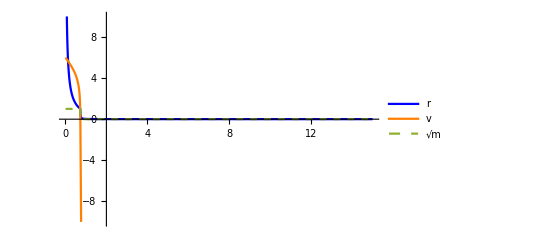

```mathematica
Plot[{Evaluate[r[x]/.Sol],Evaluate[v[x]/.Sol],Evaluate[Sqrt[m[v[x]]]/.Sol]},{x,x0,ℓ/2},PlotStyle->{Blue,Orange,Dashed},PlotLegends->{"r","v","√m"},PlotRange->{{x0,ℓ/2},{-10,10}}]
```

```mathematica
gLength=Table[Partition[Flatten[Table[{{ℓ},NIntegrate[r[x]^2/.NDSolve[{EulerEquations[Action,v[x],x],EulerEquations[Action,r[x],x],r[0.01]==50,r'[0.01]==-80,v[0.01]==t,v'[0.01]==-80},{r,v},{x,0.01,ℓ/2}],{x,0.01,ℓ/2}]},{ℓ,0.01,30.01,1.00}],2],2],{t,0.01,8.01,1}];
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.010280174573407179264804278684408700428321026265621185302734375}. NIntegrate obtained 0.97256 and 8.34061×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.0103033247458405846489794266407358236392610706388950347900390625}. NIntegrate obtained 0.972567 and 0.000774563 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.0103309248137059699642996413171402991793002001941204071044921875}. NIntegrate obtained 0.972554 and 0.000897601 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

Power::infy: Infinite expression 1/0. encountered.

NDSolve::nlnum: The function value {-0.0012451, 0.00494016, -6321.73, ComplexInfinity} is not a list of numbers with dimensions {4} at xr[x]SuperscriptBox[v[x]SuperscriptBox[ = {0.526137, 0.000627625, -0.0012451, -3184.74, -6321.73}.

Power::infy: Infinite expression 1/0. encountered.

NDSolve::nlnum: The function value {-0.00160533, 0.0118745, -17041.6, ComplexInfinity} is not a list of numbers with dimensions {4} at xr[x]SuperscriptBox[v[x]SuperscriptBox[ = {0.292719, 0.000434052, -0.00160533, -4605.84, -17041.6}.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

NDSolve::nlnum: The function value {-0.00537767, 0.119925, -46238.8, ComplexInfinity} is not a list of numbers with dimensions {4} at xr[x]SuperscriptBox[v[x]SuperscriptBox[ = {0.11213, 0.00048229, -0.00537767, -4144.97, -46238.8}.

General::stop: Further output of NDSolve :: nlnum will be suppressed during this calculation.

NDSolve::ndcf: Repeated convergence test failure at x == 0.137284; unable to continue.

NDSolve::ndcf: Repeated convergence test failure at x == 0.0316603; unable to continue.

General::stop: Further output of NDSolve :: ndcf will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0.\ ComplexInfinity encountered.

General::stop: Further output of Infinity :: indet will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NDSolve::nderr: Error test failure at x == 4.95192; unable to continue.

```mathematica
gLength
```

{{{0.1,0.0174958},{0.2,0.0188838},{0.3,0.0192797},{0.4,0.0194668},{0.5,0.0195755},{0.6,0.0196465},{0.7,0.0196963},{0.8,0.0197331},{0.9,0.0197614},{1.,0.0197837},{1.1,0.0198018},{1.2,0.0198166},{1.3,0.019829},{1.4,0.0198395},{1.5,0.0198484},{1.6,0.0198561},{1.7,0.0198628},{1.8,0.0198687},{1.9,0.0198739},{2.,0.0198784},{2.1,0.0198825},{2.2,0.0198861},{2.3,0.0198893},{2.4,0.0198922},{2.5,0.0198949},{2.6,0.0198972},{2.7,0.0198994},{2.8,0.0199013},{2.9,0.0199031},{3.,0.0199047},{3.1,0.0199062},{3.2,0.0199075},{3.3,0.0199087},{3.4,0.0199099},{3.5,0.0199109},{3.6,0.0199118},{3.7,0.0199127},{3.8,0.0199135},{3.9,0.0199142},{4.,0.0199149},{4.1,0.0199155},{4.2,0.0199161},{4.3,0.0199166},{4.4,0.0199171},{4.5,0.0199176},{4.6,0.019918},{4.7,0.0199184},{4.8,0.0199187},{4.9,0.0199191},{5.,0.0199194},{5.1,0.0199196},{5.2,0.0199199},{5.3,0.0199201},{5.4,0.0199204},{5.5,0.0199206},{5.6,0.0199208},{5.7,0.019921},{5.8,0.0199211},{5.9,0.0199213},{6.,0.0199214},{6.1,0.0199215},{6.2,0.0199217},{6.3,0.0199218},{6.4,0.0199219},{6.5,0.019922},{6.6,0.0199221},{6.7,0.0199222},{6.8,0.0199222},{6.9,0.0199223},{7.,0.0199224},{7.1,0.0199224},{7.2,0.0199225},{7.3,0.0199225},{7.4,0.0199226},{7.5,0.0199226},{7.6,0.0199227},{7.7,0.0199227},{7.8,0.0199228},{7.9,0.0199228},{8.,0.0199228},{8.1,0.0199228}},{{0.1,0.0174961},{0.2,0.0188834},{0.3,0.0192785},{0.4,0.0194648},{0.5,0.0195728},{0.6,0.019643},{0.7,0.0196921},{0.8,0.0197282},{0.9,0.0197557},{1.,0.0197773},{1.1,0.0197946},{1.2,0.0198088},{1.3,0.0198205},{1.4,0.0198303},{1.5,0.0198386},{1.6,0.0198456},{1.7,0.0198517},{1.8,0.0198569},{1.9,0.0198615},{2.,0.0198655},{2.1,0.019869},{2.2,0.019872},{2.3,0.0198747},{2.4,0.0198771},{2.5,0.0198793},{2.6,0.0198811},{2.7,0.0198828},{2.8,0.0198843},{2.9,0.0198856},{3.,0.0198868},{3.1,0.0198879},{3.2,0.0198889},{3.3,0.0198897},{3.4,0.0198905},{3.5,0.0198912},{3.6,0.0198918},{3.7,0.0198924},{3.8,0.0198929},{3.9,0.0198933},{4.,0.0198937},{4.1,0.0198941},{4.2,0.0198944},{4.3,0.0198947},{4.4,0.019895},{4.5,0.0198953},{4.6,0.0198955},{4.7,0.0198957},{4.8,0.0198959},{4.9,0.019896},{5.,0.0198962},{5.1,0.0198963},{5.2,0.0198964},{5.3,0.0198965},{5.4,0.0198966},{5.5,0.0198967},{5.6,0.0198968},{5.7,0.0198969},{5.8,0.0198969},{5.9,0.019897},{6.,0.0198971},{6.1,0.0198971},{6.2,0.0198971},{6.3,0.0198972},{6.4,0.0198972},{6.5,0.0198973},{6.6,0.0198973},{6.7,0.0198973},{6.8,0.0198973},{6.9,0.0198974},{7.,0.0198974},{7.1,0.0198974},{7.2,0.0198974},{7.3,0.0198974},{7.4,0.0198974},{7.5,0.0198975},{7.6,0.0198975},{7.7,0.0198975},{7.8,0.0198975},{7.9,0.0198975},{8.,0.0198975},{8.1,0.0198975}},{{0.1,0.0174961},{0.2,0.0188834},{0.3,0.0192785},{0.4,0.0194648},{0.5,0.0195728},{0.6,0.019643},{0.7,0.0196921},{0.8,0.0197282},{0.9,0.0197557},{1.,0.0197773},{1.1,0.0197946},{1.2,0.0198087},{1.3,0.0198204},{1.4,0.0198302},{1.5,0.0198385},{1.6,0.0198456},{1.7,0.0198516},{1.8,0.0198569},{1.9,0.0198614},{2.,0.0198654},{2.1,0.0198689},{2.2,0.019872},{2.3,0.0198747},{2.4,0.0198771},{2.5,0.0198792},{2.6,0.0198811},{2.7,0.0198827},{2.8,0.0198842},{2.9,0.0198856},{3.,0.0198868},{3.1,0.0198878},{3.2,0.0198888},{3.3,0.0198896},{3.4,0.0198904},{3.5,0.0198911},{3.6,0.0198917},{3.7,0.0198923},{3.8,0.0198928},{3.9,0.0198932},{4.,0.0198937},{4.1,0.019894},{4.2,0.0198944},{4.3,0.0198947},{4.4,0.0198949},{4.5,0.0198952},{4.6,0.0198954},{4.7,0.0198956},{4.8,0.0198958},{4.9,0.0198959},{5.,0.0198961},{5.1,0.0198962},{5.2,0.0198963},{5.3,0.0198964},{5.4,0.0198965},{5.5,0.0198966},{5.6,0.0198967},{5.7,0.0198968},{5.8,0.0198968},{5.9,0.0198969},{6.,0.019897},{6.1,0.019897},{6.2,0.019897},{6.3,0.0198971},{6.4,0.0198971},{6.5,0.0198972},{6.6,0.0198972},{6.7,0.0198972},{6.8,0.0198972},{6.9,0.0198973},{7.,0.0198973},{7.1,0.0198973},{7.2,0.0198973},{7.3,0.0198973},{7.4,0.0198973},{7.5,0.0198973},{7.6,0.0198974},{7.7,0.0198974},{7.8,0.0198974},{7.9,0.0198974},{8.,0.0198974},{8.1,0.0198974}},{{0.1,0.0174961},{0.2,0.0188834},{0.3,0.0192785},{0.4,0.0194648},{0.5,0.0195728},{0.6,0.019643},{0.7,0.0196921},{0.8,0.0197282},{0.9,0.0197557},{1.,0.0197773},{1.1,0.0197946},{1.2,0.0198087},{1.3,0.0198204},{1.4,0.0198302},{1.5,0.0198385},{1.6,0.0198456},{1.7,0.0198516},{1.8,0.0198569},{1.9,0.0198614},{2.,0.0198654},{2.1,0.0198689},{2.2,0.019872},{2.3,0.0198747},{2.4,0.0198771},{2.5,0.0198792},{2.6,0.0198811},{2.7,0.0198827},{2.8,0.0198842},{2.9,0.0198856},{3.,0.0198868},{3.1,0.0198878},{3.2,0.0198888},{3.3,0.0198896},{3.4,0.0198904},{3.5,0.0198911},{3.6,0.0198917},{3.7,0.0198923},{3.8,0.0198928},{3.9,0.0198932},{4.,0.0198937},{4.1,0.019894},{4.2,0.0198944},{4.3,0.0198947},{4.4,0.0198949},{4.5,0.0198952},{4.6,0.0198954},{4.7,0.0198956},{4.8,0.0198958},{4.9,0.0198959},{5.,0.0198961},{5.1,0.0198962},{5.2,0.0198963},{5.3,0.0198964},{5.4,0.0198965},{5.5,0.0198966},{5.6,0.0198967},{5.7,0.0198968},{5.8,0.0198968},{5.9,0.0198969},{6.,0.019897},{6.1,0.019897},{6.2,0.019897},{6.3,0.0198971},{6.4,0.0198971},{6.5,0.0198972},{6.6,0.0198972},{6.7,0.0198972},{6.8,0.0198972},{6.9,0.0198973},{7.,0.0198973},{7.1,0.0198973},{7.2,0.0198973},{7.3,0.0198973},{7.4,0.0198973},{7.5,0.0198973},{7.6,0.0198974},{7.7,0.0198974},{7.8,0.0198974},{7.9,0.0198974},{8.,0.0198974},{8.1,0.0198974}},{{0.1,0.0174961},{0.2,0.0188834},{0.3,0.0192785},{0.4,0.0194648},{0.5,0.0195728},{0.6,0.019643},{0.7,0.0196921},{0.8,0.0197282},{0.9,0.0197557},{1.,0.0197773},{1.1,0.0197946},{1.2,0.0198087},{1.3,0.0198204},{1.4,0.0198302},{1.5,0.0198385},{1.6,0.0198456},{1.7,0.0198516},{1.8,0.0198569},{1.9,0.0198614},{2.,0.0198654},{2.1,0.0198689},{2.2,0.019872},{2.3,0.0198747},{2.4,0.0198771},{2.5,0.0198792},{2.6,0.0198811},{2.7,0.0198827},{2.8,0.0198842},{2.9,0.0198856},{3.,0.0198868},{3.1,0.0198878},{3.2,0.0198888},{3.3,0.0198896},{3.4,0.0198904},{3.5,0.0198911},{3.6,0.0198917},{3.7,0.0198923},{3.8,0.0198928},{3.9,0.0198932},{4.,0.0198937},{4.1,0.019894},{4.2,0.0198944},{4.3,0.0198947},{4.4,0.0198949},{4.5,0.0198952},{4.6,0.0198954},{4.7,0.0198956},{4.8,0.0198958},{4.9,0.0198959},{5.,0.0198961},{5.1,0.0198962},{5.2,0.0198963},{5.3,0.0198964},{5.4,0.0198965},{5.5,0.0198966},{5.6,0.0198967},{5.7,0.0198968},{5.8,0.0198968},{5.9,0.0198969},{6.,0.019897},{6.1,0.019897},{6.2,0.019897},{6.3,0.0198971},{6.4,0.0198971},{6.5,0.0198972},{6.6,0.0198972},{6.7,0.0198972},{6.8,0.0198972},{6.9,0.0198973},{7.,0.0198973},{7.1,0.0198973},{7.2,0.0198973},{7.3,0.0198973},{7.4,0.0198973},{7.5,0.0198973},{7.6,0.0198974},{7.7,0.0198974},{7.8,0.0198974},{7.9,0.0198974},{8.,0.0198974},{8.1,0.0198974}},{{0.1,0.0174961},{0.2,0.0188834},{0.3,0.0192785},{0.4,0.0194648},{0.5,0.0195728},{0.6,0.019643},{0.7,0.0196921},{0.8,0.0197282},{0.9,0.0197557},{1.,0.0197773},{1.1,0.0197946},{1.2,0.0198087},{1.3,0.0198204},{1.4,0.0198302},{1.5,0.0198385},{1.6,0.0198456},{1.7,0.0198516},{1.8,0.0198569},{1.9,0.0198614},{2.,0.0198654},{2.1,0.0198689},{2.2,0.019872},{2.3,0.0198747},{2.4,0.0198771},{2.5,0.0198792},{2.6,0.0198811},{2.7,0.0198827},{2.8,0.0198842},{2.9,0.0198856},{3.,0.0198868},{3.1,0.0198878},{3.2,0.0198888},{3.3,0.0198896},{3.4,0.0198904},{3.5,0.0198911},{3.6,0.0198917},{3.7,0.0198923},{3.8,0.0198928},{3.9,0.0198932},{4.,0.0198937},{4.1,0.019894},{4.2,0.0198944},{4.3,0.0198947},{4.4,0.0198949},{4.5,0.0198952},{4.6,0.0198954},{4.7,0.0198956},{4.8,0.0198958},{4.9,0.0198959},{5.,0.0198961},{5.1,0.0198962},{5.2,0.0198963},{5.3,0.0198964},{5.4,0.0198965},{5.5,0.0198966},{5.6,0.0198967},{5.7,0.0198968},{5.8,0.0198968},{5.9,0.0198969},{6.,0.019897},{6.1,0.019897},{6.2,0.019897},{6.3,0.0198971},{6.4,0.0198971},{6.5,0.0198972},{6.6,0.0198972},{6.7,0.0198972},{6.8,0.0198972},{6.9,0.0198973},{7.,0.0198973},{7.1,0.0198973},{7.2,0.0198973},{7.3,0.0198973},{7.4,0.0198973},{7.5,0.0198973},{7.6,0.0198974},{7.7,0.0198974},{7.8,0.0198974},{7.9,0.0198974},{8.,0.0198974},{8.1,0.0198974}},{{0.1,0.0174961},{0.2,0.0188834},{0.3,0.0192785},{0.4,0.0194648},{0.5,0.0195728},{0.6,0.019643},{0.7,0.0196921},{0.8,0.0197282},{0.9,0.0197557},{1.,0.0197773},{1.1,0.0197946},{1.2,0.0198087},{1.3,0.0198204},{1.4,0.0198302},{1.5,0.0198385},{1.6,0.0198456},{1.7,0.0198516},{1.8,0.0198569},{1.9,0.0198614},{2.,0.0198654},{2.1,0.0198689},{2.2,0.019872},{2.3,0.0198747},{2.4,0.0198771},{2.5,0.0198792},{2.6,0.0198811},{2.7,0.0198827},{2.8,0.0198842},{2.9,0.0198856},{3.,0.0198868},{3.1,0.0198878},{3.2,0.0198888},{3.3,0.0198896},{3.4,0.0198904},{3.5,0.0198911},{3.6,0.0198917},{3.7,0.0198923},{3.8,0.0198928},{3.9,0.0198932},{4.,0.0198937},{4.1,0.019894},{4.2,0.0198944},{4.3,0.0198947},{4.4,0.0198949},{4.5,0.0198952},{4.6,0.0198954},{4.7,0.0198956},{4.8,0.0198958},{4.9,0.0198959},{5.,0.0198961},{5.1,0.0198962},{5.2,0.0198963},{5.3,0.0198964},{5.4,0.0198965},{5.5,0.0198966},{5.6,0.0198967},{5.7,0.0198968},{5.8,0.0198968},{5.9,0.0198969},{6.,0.019897},{6.1,0.019897},{6.2,0.019897},{6.3,0.0198971},{6.4,0.0198971},{6.5,0.0198972},{6.6,0.0198972},{6.7,0.0198972},{6.8,0.0198972},{6.9,0.0198973},{7.,0.0198973},{7.1,0.0198973},{7.2,0.0198973},{7.3,0.0198973},{7.4,0.0198973},{7.5,0.0198973},{7.6,0.0198974},{7.7,0.0198974},{7.8,0.0198974},{7.9,0.0198974},{8.,0.0198974},{8.1,0.0198974}},{{0.1,0.0174961},{0.2,0.0188834},{0.3,0.0192785},{0.4,0.0194648},{0.5,0.0195728},{0.6,0.019643},{0.7,0.0196921},{0.8,0.0197282},{0.9,0.0197557},{1.,0.0197773},{1.1,0.0197946},{1.2,0.0198087},{1.3,0.0198204},{1.4,0.0198302},{1.5,0.0198385},{1.6,0.0198456},{1.7,0.0198516},{1.8,0.0198569},{1.9,0.0198614},{2.,0.0198654},{2.1,0.0198689},{2.2,0.019872},{2.3,0.0198747},{2.4,0.0198771},{2.5,0.0198792},{2.6,0.0198811},{2.7,0.0198827},{2.8,0.0198842},{2.9,0.0198856},{3.,0.0198868},{3.1,0.0198878},{3.2,0.0198888},{3.3,0.0198896},{3.4,0.0198904},{3.5,0.0198911},{3.6,0.0198917},{3.7,0.0198923},{3.8,0.0198928},{3.9,0.0198932},{4.,0.0198937},{4.1,0.019894},{4.2,0.0198944},{4.3,0.0198947},{4.4,0.0198949},{4.5,0.0198952},{4.6,0.0198954},{4.7,0.0198956},{4.8,0.0198958},{4.9,0.0198959},{5.,0.0198961},{5.1,0.0198962},{5.2,0.0198963},{5.3,0.0198964},{5.4,0.0198965},{5.5,0.0198966},{5.6,0.0198967},{5.7,0.0198968},{5.8,0.0198968},{5.9,0.0198969},{6.,0.019897},{6.1,0.019897},{6.2,0.019897},{6.3,0.0198971},{6.4,0.0198971},{6.5,0.0198972},{6.6,0.0198972},{6.7,0.0198972},{6.8,0.0198972},{6.9,0.0198973},{7.,0.0198973},{7.1,0.0198973},{7.2,0.0198973},{7.3,0.0198973},{7.4,0.0198973},{7.5,0.0198973},{7.6,0.0198974},{7.7,0.0198974},{7.8,0.0198974},{7.9,0.0198974},{8.,0.0198974},{8.1,0.0198974}},{{0.1,0.0174961},{0.2,0.0188834},{0.3,0.0192785},{0.4,0.0194648},{0.5,0.0195728},{0.6,0.019643},{0.7,0.0196921},{0.8,0.0197282},{0.9,0.0197557},{1.,0.0197773},{1.1,0.0197946},{1.2,0.0198087},{1.3,0.0198204},{1.4,0.0198302},{1.5,0.0198385},{1.6,0.0198456},{1.7,0.0198516},{1.8,0.0198569},{1.9,0.0198614},{2.,0.0198654},{2.1,0.0198689},{2.2,0.019872},{2.3,0.0198747},{2.4,0.0198771},{2.5,0.0198792},{2.6,0.0198811},{2.7,0.0198827},{2.8,0.0198842},{2.9,0.0198856},{3.,0.0198868},{3.1,0.0198878},{3.2,0.0198888},{3.3,0.0198896},{3.4,0.0198904},{3.5,0.0198911},{3.6,0.0198917},{3.7,0.0198923},{3.8,0.0198928},{3.9,0.0198932},{4.,0.0198937},{4.1,0.019894},{4.2,0.0198944},{4.3,0.0198947},{4.4,0.0198949},{4.5,0.0198952},{4.6,0.0198954},{4.7,0.0198956},{4.8,0.0198958},{4.9,0.0198959},{5.,0.0198961},{5.1,0.0198962},{5.2,0.0198963},{5.3,0.0198964},{5.4,0.0198965},{5.5,0.0198966},{5.6,0.0198967},{5.7,0.0198968},{5.8,0.0198968},{5.9,0.0198969},{6.,0.019897},{6.1,0.019897},{6.2,0.019897},{6.3,0.0198971},{6.4,0.0198971},{6.5,0.0198972},{6.6,0.0198972},{6.7,0.0198972},{6.8,0.0198972},{6.9,0.0198973},{7.,0.0198973},{7.1,0.0198973},{7.2,0.0198973},{7.3,0.0198973},{7.4,0.0198973},{7.5,0.0198973},{7.6,0.0198974},{7.7,0.0198974},{7.8,0.0198974},{7.9,0.0198974},{8.,0.0198974},{8.1,0.0198974}}}

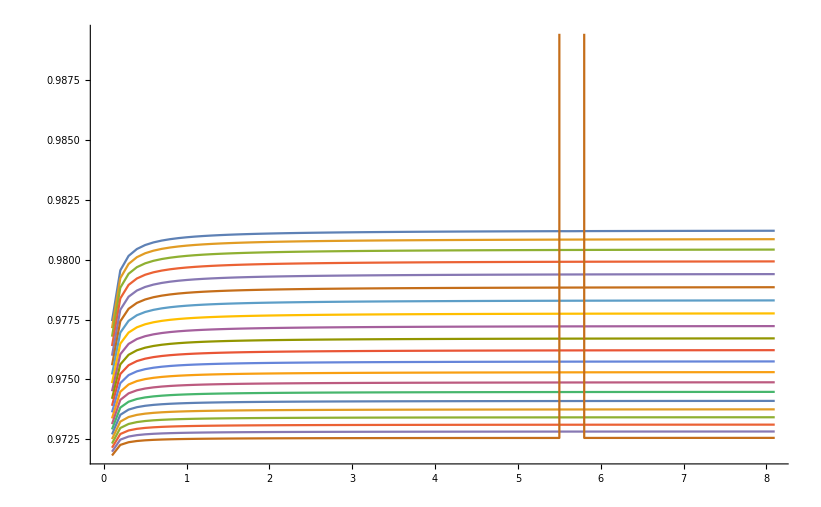

```mathematica
ListLinePlot[gLength]
```